# Calcolo della risposta alla rampa per un sistema LTI-TC

```mathematica
Clear["Global`*"]
```

```mathematica
A = {{0, 1/2, 0, 1/2}, {-10, -11, 14, 9}, {-10, -11, 14, 10}, {8, 9, -12, -9}}; B = {{0}, {1}, {1}, {-1}}; C1 = {{1, -1/2, 0, -1/2}};
```

```mathematica
G[s_]:=Simplify[(C1.Inverse[s IdentityMatrix[4]-A].B)[[1]][[1]]]
```

La risposta alla rampa (unitaria) e’ pari a G(s) (1/s^2)

```mathematica
yrampas=G[s](1/s^2)
```

(-1+s)/(s^2 (2+3 s+s^2)^2)

Scrittura dei fratti semplici della risposta alla rampa

```mathematica
Subscript[C, 11](1/s)+Subscript[C, 12](1/s^2)+Subscript[C, 21](1/(s+1))+Subscript[C, 22](1/(s+1)^2)+Subscript[C, 31](1/(s+2))+Subscript[C, 32](1/(s+2)^2)
```

-1/s^2+1/s-1/(2 (1+s)^2)-5/(4 (1+s))+C_31/(2+s)+C_32/(2+s)^2

```mathematica
Subscript[C, 12]=lim_(s->0) s^2 yrampas
```

-1/4

```mathematica
Subscript[C, 11]=lim_(s->0) D[s^2 yrampas,s]
```

1

```mathematica
Subscript[C, 22]=lim_(s->-1) (s+1)^2 yrampas
```

-2

```mathematica
Subscript[C, 21]=lim_(s->-1) D[(s+1)^2 yrampas,s]
```

1

```mathematica
Subscript[C, 32]=lim_(s->-2) (s+2)^2 yrampas
```

-3/4

```mathematica
Subscript[C, 31]=lim_(s->-2) D[(s+2)^2 yrampas,s]
```

-2

```mathematica
Subscript[C, 11](1/s)+Subscript[C, 12](1/s^2)+Subscript[C, 21](1/(s+1))+Subscript[C, 22](1/(s+1)^2)+Subscript[C, 31](1/(s+2))+Subscript[C, 32](1/(s+2)^2)
```

-1/(4 s^2)+1/s-2/(1+s)^2+1/(1+s)-3/(4 (2+s)^2)-2/(2+s)

```mathematica
Subscript[y, -2][t_]:=Subscript[C, 11] UnitStep[t]+Subscript[C, 12] t UnitStep[t]+Subscript[C, 21] Exp[-t]UnitStep[t]+Subscript[C, 22] t Exp[-t]UnitStep[t]+Subscript[C, 31] Exp[-2t]UnitStep[t]+Subscript[C, 32] t Exp[-2t]UnitStep[t]
```

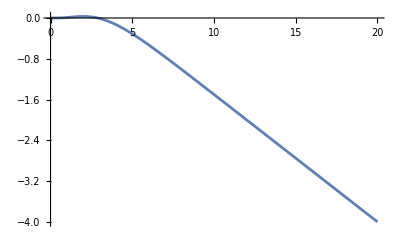

```mathematica
Plot[Subscript[y, -2][t],{t,0,20},PlotRange->All]
```

```mathematica
yss=Subscript[C, 11] UnitStep[t]+Subscript[C, 12] t UnitStep[t]
```

UnitStep[t]-1/4 t UnitStep[t]

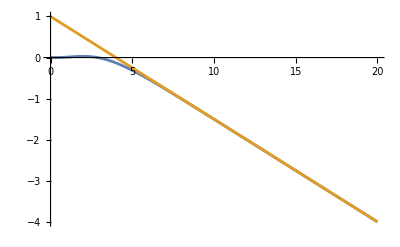

```mathematica
Plot[{Subscript[y, -2][t],yss},{t,0,20},PlotRange->All]
```